```mathematica
Sqrt[x]
```

√x

```mathematica
Sqrt[Sqrt@x]
```

x^(1/4)

```mathematica
x^(1/(2n))
```

x^(1/2/n)

```mathematica
Manipulate[Plot[x^(1/2/n),{x,-8,8}],{n,-8,8}]
```

```mathematica
Plot3D[x^(1/2/n),{x,-8,8},{n,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[x^(1/2/n),{x,-8,8},{n,0,8}]
```

-Graphics3D-

```mathematica
Plot3D[x^(1/2/n),{x,0,8},{n,0,8}]
```

General::munfl: 0.000572^874.126 is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
NestList[1/(1+#)&,α,10]
```

{α,1/(1+α),1/(1+1/(1+α)),1/(1+1/(1+1/(1+α))),1/(1+1/(1+1/(1+1/(1+α)))),1/(1+1/(1+1/(1+1/(1+1/(1+α))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+α)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+α))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+α)))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+α))))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+α))))))))))}

```mathematica
NestList[1/(1+#)&,1,10]
```

{1,1/2,2/3,3/5,5/8,8/13,13/21,21/34,34/55,55/89,89/144}

```mathematica
N@NestList[1/(1+#)&,1,10]
```

{1.,0.5,0.666667,0.6,0.625,0.615385,0.619048,0.617647,0.618182,0.617978,0.618056}

```mathematica
1==1/(1+ϕ)
```

1==1/(1+ϕ)

```mathematica
Reduce[1==1/(1+ϕ)]
```

ϕ==0

```mathematica
ϕ==1/(1+ϕ)
```

ϕ==1/(1+ϕ)

```mathematica
Reduce[ϕ==1/(1+ϕ)]
```

ϕ==1/2 (-1-√5)||ϕ==1/2 (-1+√5)

```mathematica
FullSimplify[NestList[1/(1+#)&,α,10],α∈Reals]
```

{α,1/(1+α),(1+α)/(2+α),(2+α)/(3+2 α),(3+2 α)/(5+3 α),(5+3 α)/(8+5 α),(8+5 α)/(13+8 α),(13+8 α)/(21+13 α),(21+13 α)/(34+21 α),(34+21 α)/(55+34 α),(55+34 α)/(89+55 α)}

```mathematica
FullSimplify[Table[{i,Nest[1/(1+#)&,α,i]},{i,1,10}],α∈Reals]
```

{{1,1/(1+α)},{2,(1+α)/(2+α)},{3,(2+α)/(3+2 α)},{4,(3+2 α)/(5+3 α)},{5,(5+3 α)/(8+5 α)},{6,(8+5 α)/(13+8 α)},{7,(13+8 α)/(21+13 α)},{8,(21+13 α)/(34+21 α)},{9,(34+21 α)/(55+34 α)},{10,(55+34 α)/(89+55 α)}}

```mathematica
Grid@
FullSimplify[Table[{i,Nest[1/(1+#)&,α,i]},{i,1,10}],α∈Reals]
```

1 | 1/(1+α)
2 | (1+α)/(2+α)
3 | (2+α)/(3+2 α)
4 | (3+2 α)/(5+3 α)
5 | (5+3 α)/(8+5 α)
6 | (8+5 α)/(13+8 α)
7 | (13+8 α)/(21+13 α)
8 | (21+13 α)/(34+21 α)
9 | (34+21 α)/(55+34 α)
10 | (55+34 α)/(89+55 α)

```mathematica
FullSimplify[Table[{i,Nest[1/(1-#)&,α,i]},{i,1,10}],α∈Reals]
```

{{1,1/(1-α)},{2,(-1+α)/α},{3,α},{4,1/(1-α)},{5,(-1+α)/α},{6,α},{7,1/(1-α)},{8,(-1+α)/α},{9,α},{10,1/(1-α)}}

```mathematica
((-1)^(n+1)f[x])^((-1)^(n+1))
```

((-1)^(1+n) f[x])^((-1)^(1+n))

```mathematica
Table[((-1)^(n+1)f[x])^((-1)^(n+1)),{n,1,10,1}]
```

{f[x],-1/f[x],f[x],-1/f[x],f[x],-1/f[x],f[x],-1/f[x],f[x],-1/f[x]}

```mathematica
FullSimplify[NestList[1/(1+#)&,1/2 (-1+√5),10],α∈Reals]
```

{1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5),1/2 (-1+√5)}

```mathematica
ComplexPlot[1/(1+z),{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
{ComplexPlot[z,{z,-5-5I,5+5I}],ComplexPlot[1/(1+z),{z,-5-5I,5+5I}]}
```

{-Graphics-,-Graphics-}

```mathematica
ComplexPlot[z^3,{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
ComplexPlot[z^4,{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
Limit[α/(1+α),α->∞]
```

1

```mathematica
Limit[α/(2+α),α->∞]
```

1

```mathematica
Limit[(2α)/(1+α),α->∞]
```

2

```mathematica
Limit[α/(1+2α),α->∞]
```

1/2

```mathematica
Series[α/(1+2α),{α,0,10}]
```

α-2 α^2+4 α^3-8 α^4+16 α^5-32 α^6+64 α^7-128 α^8+256 α^9-512 α^10+O[α]^11

```mathematica
Series[1/(1+α),{α,0,10}]
```

1-α+α^2-α^3+α^4-α^5+α^6-α^7+α^8-α^9+α^10+O[α]^11

```mathematica
Series[1/(1+α),{}]
```

Series::sspec: Series specification {} is not a list with three elements.

Series[1/(1+α),{}]

```mathematica
Table[(-1)^n α^n,{x,0,10,1}]
```

{(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n,(-1)^n α^n}

```mathematica
FullSimplify[Table[(-1)^n α^n,{n,0,10,1}],α∈Reals∧n∈]
```

{1,-α,α^2,-α^3,α^4,-α^5,α^6,-α^7,α^8,-α^9,α^10}

```mathematica
FullSimplify[Total@Table[(-1)^n α^n,{n,0,10,1}],α∈Reals∧n∈]
```

1+(-1+α) α (1+α+α^2+α^3+α^4) (1+(-1+α) α (1+α^2))

```mathematica
FullSimplify[Total@Table[(-1)^n α^n,{n,0,10,1}],α∈Reals]
```

1+(-1+α) α (1+α+α^2+α^3+α^4) (1+(-1+α) α (1+α^2))

```mathematica
FullSimplify[Total@Table[(-1)^n α^n,{n,0,10,1}],α∈Reals]/.α->1
```

1

```mathematica
FullSimplify[Total@Table[(-1)^n α^n,{n,0,10,1}],α∈Reals]/.α->2
```

683

```mathematica
FullSimplify[Total@Table[(-1)^n α^n,{n,0,10,1}],α∈Reals]/.α->3
```

44287

```mathematica
NestList[1/(1+#)&,√5,10]
```

{√5,1/(1+√5),1/(1+1/(1+√5)),1/(1+1/(1+1/(1+√5))),1/(1+1/(1+1/(1+1/(1+√5)))),1/(1+1/(1+1/(1+1/(1+1/(1+√5))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+√5)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+√5))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+√5)))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+√5))))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+√5))))))))))}

```mathematica
FullSimplify[NestList[1/(1+#)&,√5,10]]
```

{√5,1/(1+√5),3-√5,1/11 (4+√5),3/4-1/(4 √5),1/61 (35+√5),1/151 (96-√5),1/404 (247+√5),(651-√5)/1049,(1700+√5)/2755,(4455-√5)/7204}

```mathematica
N[NestList[1/(1+#)&,√5,10]]
```

{2.23607,0.309017,0.763932,0.566915,0.638197,0.610427,0.620953,0.616921,0.618459,0.617872,0.618096}

```mathematica
N[NestList[1/(1+#)&,√5,50]]
```

{2.23607,0.309017,0.763932,0.566915,0.638197,0.610427,0.620953,0.616921,0.618459,0.617872,0.618096,0.61801,0.618043,0.618031,0.618035,0.618033,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034}

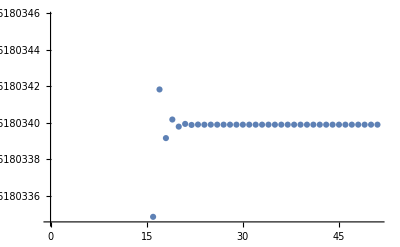

```mathematica
ListPlot[%44]
```

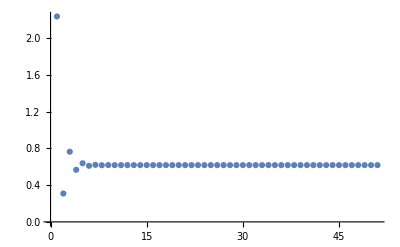

```mathematica
ListPlot[%44,PlotRange->Full]
```

```mathematica
FullSimplify[Table[{i,Nest[1/(1+#)&,α,i]},{i,1,20}],α∈Reals]
```

{{1,1/(1+α)},{2,(1+α)/(2+α)},{3,(2+α)/(3+2 α)},{4,(3+2 α)/(5+3 α)},{5,(5+3 α)/(8+5 α)},{6,(8+5 α)/(13+8 α)},{7,(13+8 α)/(21+13 α)},{8,(21+13 α)/(34+21 α)},{9,(34+21 α)/(55+34 α)},{10,(55+34 α)/(89+55 α)},{11,(89+55 α)/(144+89 α)},{12,(144+89 α)/(233+144 α)},{13,(233+144 α)/(377+233 α)},{14,(377+233 α)/(610+377 α)},{15,(610+377 α)/(987+610 α)},{16,(987+610 α)/(1597+987 α)},{17,(1597+987 α)/(2584+1597 α)},{18,(2584+1597 α)/(4181+2584 α)},{19,(4181+2584 α)/(6765+4181 α)},{20,(6765+4181 α)/(10946+6765 α)}}

```mathematica
FullSimplify[NestList[1/(1+#)&,α,100],α∈Reals]
```

{α,1/(1+α),(1+α)/(2+α),(2+α)/(3+2 α),(3+2 α)/(5+3 α),(5+3 α)/(8+5 α),(8+5 α)/(13+8 α),(13+8 α)/(21+13 α),(21+13 α)/(34+21 α),(34+21 α)/(55+34 α),(55+34 α)/(89+55 α),(89+55 α)/(144+89 α),(144+89 α)/(233+144 α),(233+144 α)/(377+233 α),(377+233 α)/(610+377 α),(610+377 α)/(987+610 α),(987+610 α)/(1597+987 α),(1597+987 α)/(2584+1597 α),(2584+1597 α)/(4181+2584 α),(4181+2584 α)/(6765+4181 α),(6765+4181 α)/(10946+6765 α),(10946+6765 α)/(17711+10946 α),(17711+10946 α)/(28657+17711 α),(28657+17711 α)/(46368+28657 α),(46368+28657 α)/(75025+46368 α),(75025+46368 α)/(121393+75025 α),(121393+75025 α)/(196418+121393 α),(196418+121393 α)/(317811+196418 α),(317811+196418 α)/(514229+317811 α),(514229+317811 α)/(832040+514229 α),(832040+514229 α)/(1346269+832040 α),(1346269+832040 α)/(2178309+1346269 α),(2178309+1346269 α)/(3524578+2178309 α),(3524578+2178309 α)/(5702887+3524578 α),(5702887+3524578 α)/(9227465+5702887 α),(9227465+5702887 α)/(14930352+9227465 α),(14930352+9227465 α)/(24157817+14930352 α),(24157817+14930352 α)/(39088169+24157817 α),(39088169+24157817 α)/(63245986+39088169 α),(63245986+39088169 α)/(102334155+63245986 α),(102334155+63245986 α)/(165580141+102334155 α),(165580141+102334155 α)/(267914296+165580141 α),(267914296+165580141 α)/(433494437+267914296 α),(433494437+267914296 α)/(701408733+433494437 α),(701408733+433494437 α)/(1134903170+701408733 α),(1134903170+701408733 α)/(1836311903+1134903170 α),(1836311903+1134903170 α)/(2971215073+1836311903 α),(2971215073+1836311903 α)/(4807526976+2971215073 α),(4807526976+2971215073 α)/(7778742049+4807526976 α),(7778742049+4807526976 α)/(12586269025+7778742049 α),(12586269025+7778742049 α)/(20365011074+12586269025 α),(20365011074+12586269025 α)/(32951280099+20365011074 α),(32951280099+20365011074 α)/(53316291173+32951280099 α),(53316291173+32951280099 α)/(86267571272+53316291173 α),(86267571272+53316291173 α)/(139583862445+86267571272 α),(139583862445+86267571272 α)/(225851433717+139583862445 α),(225851433717+139583862445 α)/(365435296162+225851433717 α),(365435296162+225851433717 α)/(591286729879+365435296162 α),(591286729879+365435296162 α)/(956722026041+591286729879 α),(956722026041+591286729879 α)/(1548008755920+956722026041 α),(1548008755920+956722026041 α)/(2504730781961+1548008755920 α),(2504730781961+1548008755920 α)/(4052739537881+2504730781961 α),(4052739537881+2504730781961 α)/(6557470319842+4052739537881 α),(6557470319842+4052739537881 α)/(10610209857723+6557470319842 α),(10610209857723+6557470319842 α)/(17167680177565+10610209857723 α),(17167680177565+10610209857723 α)/(27777890035288+17167680177565 α),(27777890035288+17167680177565 α)/(44945570212853+27777890035288 α),(44945570212853+27777890035288 α)/(72723460248141+44945570212853 α),(72723460248141+44945570212853 α)/(117669030460994+72723460248141 α),(117669030460994+72723460248141 α)/(190392490709135+117669030460994 α),(190392490709135+117669030460994 α)/(308061521170129+190392490709135 α),(308061521170129+190392490709135 α)/(498454011879264+308061521170129 α),(498454011879264+308061521170129 α)/(806515533049393+498454011879264 α),(806515533049393+498454011879264 α)/(1304969544928657+806515533049393 α),(1304969544928657+806515533049393 α)/(2111485077978050+1304969544928657 α),(2111485077978050+1304969544928657 α)/(3416454622906707+2111485077978050 α),(3416454622906707+2111485077978050 α)/(5527939700884757+3416454622906707 α),(5527939700884757+3416454622906707 α)/(8944394323791464+5527939700884757 α),(8944394323791464+5527939700884757 α)/(14472334024676221+8944394323791464 α),(14472334024676221+8944394323791464 α)/(23416728348467685+14472334024676221 α),(23416728348467685+14472334024676221 α)/(37889062373143906+23416728348467685 α),(37889062373143906+23416728348467685 α)/(61305790721611591+37889062373143906 α),(61305790721611591+37889062373143906 α)/(99194853094755497+61305790721611591 α),(99194853094755497+61305790721611591 α)/(160500643816367088+99194853094755497 α),(160500643816367088+99194853094755497 α)/(259695496911122585+160500643816367088 α),(259695496911122585+160500643816367088 α)/(420196140727489673+259695496911122585 α),(420196140727489673+259695496911122585 α)/(679891637638612258+420196140727489673 α),(679891637638612258+420196140727489673 α)/(1100087778366101931+679891637638612258 α),(1100087778366101931+679891637638612258 α)/(1779979416004714189+1100087778366101931 α),(1779979416004714189+1100087778366101931 α)/(2880067194370816120+1779979416004714189 α),(2880067194370816120+1779979416004714189 α)/(4660046610375530309+2880067194370816120 α),(4660046610375530309+2880067194370816120 α)/(7540113804746346429+4660046610375530309 α),(7540113804746346429+4660046610375530309 α)/(12200160415121876738+7540113804746346429 α),(12200160415121876738+7540113804746346429 α)/(19740274219868223167+12200160415121876738 α),(19740274219868223167+12200160415121876738 α)/(31940434634990099905+19740274219868223167 α),(31940434634990099905+19740274219868223167 α)/(51680708854858323072+31940434634990099905 α),(51680708854858323072+31940434634990099905 α)/(83621143489848422977+51680708854858323072 α),(83621143489848422977+51680708854858323072 α)/(135301852344706746049+83621143489848422977 α),(135301852344706746049+83621143489848422977 α)/(218922995834555169026+135301852344706746049 α),(218922995834555169026+135301852344706746049 α)/(354224848179261915075+218922995834555169026 α),(354224848179261915075+218922995834555169026 α)/(573147844013817084101+354224848179261915075 α)}

```mathematica
Out[48]/.α->1
```

{1,1/2,2/3,3/5,5/8,8/13,13/21,21/34,34/55,55/89,89/144,144/233,233/377,377/610,610/987,987/1597,1597/2584,2584/4181,4181/6765,6765/10946,10946/17711,17711/28657,28657/46368,46368/75025,75025/121393,121393/196418,196418/317811,317811/514229,514229/832040,832040/1346269,1346269/2178309,2178309/3524578,3524578/5702887,5702887/9227465,9227465/14930352,14930352/24157817,24157817/39088169,39088169/63245986,63245986/102334155,102334155/165580141,165580141/267914296,267914296/433494437,433494437/701408733,701408733/1134903170,1134903170/1836311903,1836311903/2971215073,2971215073/4807526976,4807526976/7778742049,7778742049/12586269025,12586269025/20365011074,20365011074/32951280099,32951280099/53316291173,53316291173/86267571272,86267571272/139583862445,139583862445/225851433717,225851433717/365435296162,365435296162/591286729879,591286729879/956722026041,956722026041/1548008755920,1548008755920/2504730781961,2504730781961/4052739537881,4052739537881/6557470319842,6557470319842/10610209857723,10610209857723/17167680177565,17167680177565/27777890035288,27777890035288/44945570212853,44945570212853/72723460248141,72723460248141/117669030460994,117669030460994/190392490709135,190392490709135/308061521170129,308061521170129/498454011879264,498454011879264/806515533049393,806515533049393/1304969544928657,1304969544928657/2111485077978050,2111485077978050/3416454622906707,3416454622906707/5527939700884757,5527939700884757/8944394323791464,8944394323791464/14472334024676221,14472334024676221/23416728348467685,23416728348467685/37889062373143906,37889062373143906/61305790721611591,61305790721611591/99194853094755497,99194853094755497/160500643816367088,160500643816367088/259695496911122585,259695496911122585/420196140727489673,420196140727489673/679891637638612258,679891637638612258/1100087778366101931,1100087778366101931/1779979416004714189,1779979416004714189/2880067194370816120,2880067194370816120/4660046610375530309,4660046610375530309/7540113804746346429,7540113804746346429/12200160415121876738,12200160415121876738/19740274219868223167,19740274219868223167/31940434634990099905,31940434634990099905/51680708854858323072,51680708854858323072/83621143489848422977,83621143489848422977/135301852344706746049,135301852344706746049/218922995834555169026,218922995834555169026/354224848179261915075,354224848179261915075/573147844013817084101,573147844013817084101/927372692193078999176}

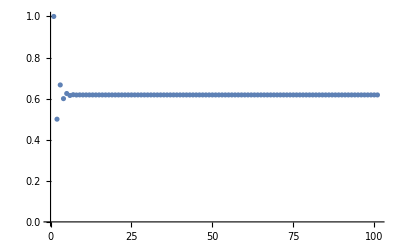

```mathematica
ListPlot[%49]
```

```mathematica
Log[1/2 (-1+√5),#]&/@Out[49]
```

{0,-Log[2]/Log[1/2 (-1+√5)],-Log[3/2]/Log[1/2 (-1+√5)],-Log[5/3]/Log[1/2 (-1+√5)],-Log[8/5]/Log[1/2 (-1+√5)],-Log[13/8]/Log[1/2 (-1+√5)],-Log[21/13]/Log[1/2 (-1+√5)],-Log[34/21]/Log[1/2 (-1+√5)],-Log[55/34]/Log[1/2 (-1+√5)],-Log[89/55]/Log[1/2 (-1+√5)],-Log[144/89]/Log[1/2 (-1+√5)],-Log[233/144]/Log[1/2 (-1+√5)],-Log[377/233]/Log[1/2 (-1+√5)],-Log[610/377]/Log[1/2 (-1+√5)],-Log[987/610]/Log[1/2 (-1+√5)],-Log[1597/987]/Log[1/2 (-1+√5)],-Log[2584/1597]/Log[1/2 (-1+√5)],-Log[4181/2584]/Log[1/2 (-1+√5)],-Log[6765/4181]/Log[1/2 (-1+√5)],-Log[10946/6765]/Log[1/2 (-1+√5)],-Log[17711/10946]/Log[1/2 (-1+√5)],-Log[28657/17711]/Log[1/2 (-1+√5)],-Log[46368/28657]/Log[1/2 (-1+√5)],-Log[75025/46368]/Log[1/2 (-1+√5)],-Log[121393/75025]/Log[1/2 (-1+√5)],-Log[196418/121393]/Log[1/2 (-1+√5)],-Log[317811/196418]/Log[1/2 (-1+√5)],-Log[514229/317811]/Log[1/2 (-1+√5)],-Log[832040/514229]/Log[1/2 (-1+√5)],-Log[1346269/832040]/Log[1/2 (-1+√5)],-Log[2178309/1346269]/Log[1/2 (-1+√5)],-Log[3524578/2178309]/Log[1/2 (-1+√5)],-Log[5702887/3524578]/Log[1/2 (-1+√5)],-Log[9227465/5702887]/Log[1/2 (-1+√5)],-Log[14930352/9227465]/Log[1/2 (-1+√5)],-Log[24157817/14930352]/Log[1/2 (-1+√5)],-Log[39088169/24157817]/Log[1/2 (-1+√5)],-Log[63245986/39088169]/Log[1/2 (-1+√5)],-Log[102334155/63245986]/Log[1/2 (-1+√5)],-Log[165580141/102334155]/Log[1/2 (-1+√5)],-Log[267914296/165580141]/Log[1/2 (-1+√5)],-Log[433494437/267914296]/Log[1/2 (-1+√5)],-Log[701408733/433494437]/Log[1/2 (-1+√5)],-Log[1134903170/701408733]/Log[1/2 (-1+√5)],-Log[1836311903/1134903170]/Log[1/2 (-1+√5)],-Log[2971215073/1836311903]/Log[1/2 (-1+√5)],-Log[4807526976/2971215073]/Log[1/2 (-1+√5)],-Log[7778742049/4807526976]/Log[1/2 (-1+√5)],-Log[12586269025/7778742049]/Log[1/2 (-1+√5)],-Log[20365011074/12586269025]/Log[1/2 (-1+√5)],-Log[32951280099/20365011074]/Log[1/2 (-1+√5)],-Log[53316291173/32951280099]/Log[1/2 (-1+√5)],-Log[86267571272/53316291173]/Log[1/2 (-1+√5)],-Log[139583862445/86267571272]/Log[1/2 (-1+√5)],-Log[225851433717/139583862445]/Log[1/2 (-1+√5)],-Log[365435296162/225851433717]/Log[1/2 (-1+√5)],-Log[591286729879/365435296162]/Log[1/2 (-1+√5)],-Log[956722026041/591286729879]/Log[1/2 (-1+√5)],-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)],-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)],-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)],-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)],-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)],-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)],-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)],-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)],-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)],-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)],-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)],-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)],-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)],-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)],-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)],-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)],-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)],-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)],-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)],-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)],-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)],-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)],-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)],-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)],-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)],-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)],-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)],-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)],-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)],-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)],-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)],-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)],-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)],-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)],-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)],-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)],-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)],-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)],-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)],-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)],-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)],-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)],-Log[927372692193078999176/573147844013817084101]/Log[1/2 (-1+√5)]}

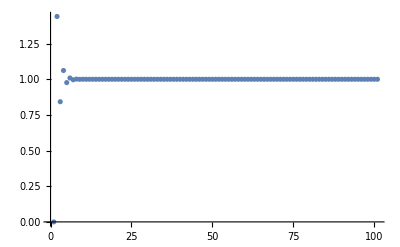

```mathematica
ListPlot[%51]
```

```mathematica
Differences@Out[49]
```

{-1/2,1/6,-1/15,1/40,-1/104,1/273,-1/714,1/1870,-1/4895,1/12816,-1/33552,1/87841,-1/229970,1/602070,-1/1576239,1/4126648,-1/10803704,1/28284465,-1/74049690,1/193864606,-1/507544127,1/1328767776,-1/3478759200,1/9107509825,-1/23843770274,1/62423800998,-1/163427632719,1/427859097160,-1/1120149658760,1/2932589879121,-1/7677619978602,1/20100270056686,-1/52623190191455,1/137769300517680,-1/360684711361584,1/944284833567073,-1/2472169789339634,1/6472224534451830,-1/16944503814015855,1/44361286907595736,-1/116139356908771352,1/304056783818718321,-1/796030994547383610,1/2084036199823432510,-1/5456077604922913919,1/14284196614945309248,-1/37396512239913013824,1/97905340104793732225,-1/256319508074468182850,1/671053184118610816326,-1/1756840044281364266127,1/4599466948725481982056,-1/12041560801895081680040,1/31525215456959763058065,-1/82534085568984207494154,1/216077041249992859424398,-1/565697038180994370779039,1/1481014073292990252912720,-1/3877345181697976387959120,1/10151021471800938910964641,-1/26575719233704840344934802,1/69576136229313582123839766,-1/182152689454235906026584495,1/476881932133394135955913720,-1/1248493106945946501841156664,1/3268597388704445369567556273,-1/8557299059167389606861512154,1/22403299788797723451016980190,-1/58652600307225780746189428415,1/153554501132879618787551305056,-1/402010903091413075616464486752,1/1052478208141359608061842155201,-1/2755423721332665748569061978850,1/7213792955856637637645343781350,-1/18885955146237247164366969365199,1/49444072482855103855455564314248,-1/129446262302328064401999723577544,1/338894714424129089350543606418385,-1/887237880970059203649631095677610,1/2322818928486048521598349680614446,-1/6081218904488086361145417946165727,1/15920837784978210561837904157882736,-1/41681294450446545324368294527482480,1/109123045566361425411266979424564705,-1/285687842248637730909432643746211634,1/747940481179551767317030951814070198,-1/1958133601290017571041660211695998959,1/5126460322690500945807949683273926680,-1/13421247366781485266382188838125781080,1/35137281777653954853338616831103416561,-1/91990597966180379293633661655184468602,1/240834512120887183027562368134449989246,-1/630512938396481169789053442748165499135,1/1650704303068556326339597960110046508160,-1/4321599970809187809229740437581974025344,1/11314095609359007101349623352635875567873,-1/29620686857267833494819129620325652678274,1/77547964962444493383107765508341082466950,-1/203023208030065646654504166904697594722575,1/531521659127752446580404735205751701700776}

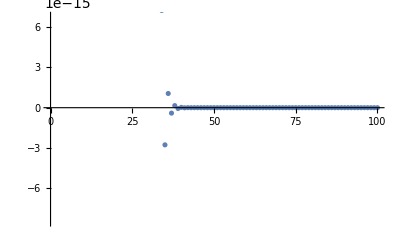

```mathematica
ListPlot[%53]
```

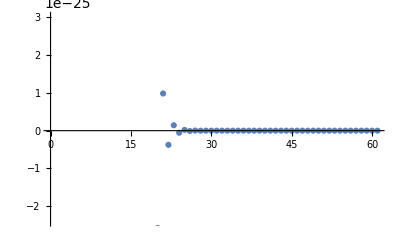

```mathematica
ListPlot[Out[53][[40;;]]]
```

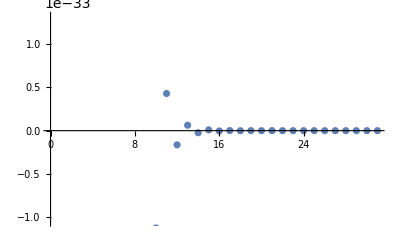

```mathematica
ListPlot[Out[53][[70;;]]]
```

```mathematica
Partition[Out[51],2,1]
```

{{0,-Log[2]/Log[1/2 (-1+√5)]},{-Log[2]/Log[1/2 (-1+√5)],-Log[3/2]/Log[1/2 (-1+√5)]},{-Log[3/2]/Log[1/2 (-1+√5)],-Log[5/3]/Log[1/2 (-1+√5)]},{-Log[5/3]/Log[1/2 (-1+√5)],-Log[8/5]/Log[1/2 (-1+√5)]},{-Log[8/5]/Log[1/2 (-1+√5)],-Log[13/8]/Log[1/2 (-1+√5)]},{-Log[13/8]/Log[1/2 (-1+√5)],-Log[21/13]/Log[1/2 (-1+√5)]},{-Log[21/13]/Log[1/2 (-1+√5)],-Log[34/21]/Log[1/2 (-1+√5)]},{-Log[34/21]/Log[1/2 (-1+√5)],-Log[55/34]/Log[1/2 (-1+√5)]},{-Log[55/34]/Log[1/2 (-1+√5)],-Log[89/55]/Log[1/2 (-1+√5)]},{-Log[89/55]/Log[1/2 (-1+√5)],-Log[144/89]/Log[1/2 (-1+√5)]},{-Log[144/89]/Log[1/2 (-1+√5)],-Log[233/144]/Log[1/2 (-1+√5)]},{-Log[233/144]/Log[1/2 (-1+√5)],-Log[377/233]/Log[1/2 (-1+√5)]},{-Log[377/233]/Log[1/2 (-1+√5)],-Log[610/377]/Log[1/2 (-1+√5)]},{-Log[610/377]/Log[1/2 (-1+√5)],-Log[987/610]/Log[1/2 (-1+√5)]},{-Log[987/610]/Log[1/2 (-1+√5)],-Log[1597/987]/Log[1/2 (-1+√5)]},{-Log[1597/987]/Log[1/2 (-1+√5)],-Log[2584/1597]/Log[1/2 (-1+√5)]},{-Log[2584/1597]/Log[1/2 (-1+√5)],-Log[4181/2584]/Log[1/2 (-1+√5)]},{-Log[4181/2584]/Log[1/2 (-1+√5)],-Log[6765/4181]/Log[1/2 (-1+√5)]},{-Log[6765/4181]/Log[1/2 (-1+√5)],-Log[10946/6765]/Log[1/2 (-1+√5)]},{-Log[10946/6765]/Log[1/2 (-1+√5)],-Log[17711/10946]/Log[1/2 (-1+√5)]},{-Log[17711/10946]/Log[1/2 (-1+√5)],-Log[28657/17711]/Log[1/2 (-1+√5)]},{-Log[28657/17711]/Log[1/2 (-1+√5)],-Log[46368/28657]/Log[1/2 (-1+√5)]},{-Log[46368/28657]/Log[1/2 (-1+√5)],-Log[75025/46368]/Log[1/2 (-1+√5)]},{-Log[75025/46368]/Log[1/2 (-1+√5)],-Log[121393/75025]/Log[1/2 (-1+√5)]},{-Log[121393/75025]/Log[1/2 (-1+√5)],-Log[196418/121393]/Log[1/2 (-1+√5)]},{-Log[196418/121393]/Log[1/2 (-1+√5)],-Log[317811/196418]/Log[1/2 (-1+√5)]},{-Log[317811/196418]/Log[1/2 (-1+√5)],-Log[514229/317811]/Log[1/2 (-1+√5)]},{-Log[514229/317811]/Log[1/2 (-1+√5)],-Log[832040/514229]/Log[1/2 (-1+√5)]},{-Log[832040/514229]/Log[1/2 (-1+√5)],-Log[1346269/832040]/Log[1/2 (-1+√5)]},{-Log[1346269/832040]/Log[1/2 (-1+√5)],-Log[2178309/1346269]/Log[1/2 (-1+√5)]},{-Log[2178309/1346269]/Log[1/2 (-1+√5)],-Log[3524578/2178309]/Log[1/2 (-1+√5)]},{-Log[3524578/2178309]/Log[1/2 (-1+√5)],-Log[5702887/3524578]/Log[1/2 (-1+√5)]},{-Log[5702887/3524578]/Log[1/2 (-1+√5)],-Log[9227465/5702887]/Log[1/2 (-1+√5)]},{-Log[9227465/5702887]/Log[1/2 (-1+√5)],-Log[14930352/9227465]/Log[1/2 (-1+√5)]},{-Log[14930352/9227465]/Log[1/2 (-1+√5)],-Log[24157817/14930352]/Log[1/2 (-1+√5)]},{-Log[24157817/14930352]/Log[1/2 (-1+√5)],-Log[39088169/24157817]/Log[1/2 (-1+√5)]},{-Log[39088169/24157817]/Log[1/2 (-1+√5)],-Log[63245986/39088169]/Log[1/2 (-1+√5)]},{-Log[63245986/39088169]/Log[1/2 (-1+√5)],-Log[102334155/63245986]/Log[1/2 (-1+√5)]},{-Log[102334155/63245986]/Log[1/2 (-1+√5)],-Log[165580141/102334155]/Log[1/2 (-1+√5)]},{-Log[165580141/102334155]/Log[1/2 (-1+√5)],-Log[267914296/165580141]/Log[1/2 (-1+√5)]},{-Log[267914296/165580141]/Log[1/2 (-1+√5)],-Log[433494437/267914296]/Log[1/2 (-1+√5)]},{-Log[433494437/267914296]/Log[1/2 (-1+√5)],-Log[701408733/433494437]/Log[1/2 (-1+√5)]},{-Log[701408733/433494437]/Log[1/2 (-1+√5)],-Log[1134903170/701408733]/Log[1/2 (-1+√5)]},{-Log[1134903170/701408733]/Log[1/2 (-1+√5)],-Log[1836311903/1134903170]/Log[1/2 (-1+√5)]},{-Log[1836311903/1134903170]/Log[1/2 (-1+√5)],-Log[2971215073/1836311903]/Log[1/2 (-1+√5)]},{-Log[2971215073/1836311903]/Log[1/2 (-1+√5)],-Log[4807526976/2971215073]/Log[1/2 (-1+√5)]},{-Log[4807526976/2971215073]/Log[1/2 (-1+√5)],-Log[7778742049/4807526976]/Log[1/2 (-1+√5)]},{-Log[7778742049/4807526976]/Log[1/2 (-1+√5)],-Log[12586269025/7778742049]/Log[1/2 (-1+√5)]},{-Log[12586269025/7778742049]/Log[1/2 (-1+√5)],-Log[20365011074/12586269025]/Log[1/2 (-1+√5)]},{-Log[20365011074/12586269025]/Log[1/2 (-1+√5)],-Log[32951280099/20365011074]/Log[1/2 (-1+√5)]},{-Log[32951280099/20365011074]/Log[1/2 (-1+√5)],-Log[53316291173/32951280099]/Log[1/2 (-1+√5)]},{-Log[53316291173/32951280099]/Log[1/2 (-1+√5)],-Log[86267571272/53316291173]/Log[1/2 (-1+√5)]},{-Log[86267571272/53316291173]/Log[1/2 (-1+√5)],-Log[139583862445/86267571272]/Log[1/2 (-1+√5)]},{-Log[139583862445/86267571272]/Log[1/2 (-1+√5)],-Log[225851433717/139583862445]/Log[1/2 (-1+√5)]},{-Log[225851433717/139583862445]/Log[1/2 (-1+√5)],-Log[365435296162/225851433717]/Log[1/2 (-1+√5)]},{-Log[365435296162/225851433717]/Log[1/2 (-1+√5)],-Log[591286729879/365435296162]/Log[1/2 (-1+√5)]},{-Log[591286729879/365435296162]/Log[1/2 (-1+√5)],-Log[956722026041/591286729879]/Log[1/2 (-1+√5)]},{-Log[956722026041/591286729879]/Log[1/2 (-1+√5)],-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)]},{-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)],-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)]},{-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)],-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)]},{-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)],-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)]},{-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)],-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)]},{-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)],-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)]},{-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)],-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)]},{-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)],-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)]},{-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)],-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)]},{-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)],-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)]},{-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)],-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)]},{-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)],-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)]},{-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)],-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)]},{-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)],-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)]},{-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)],-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)]},{-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)],-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)]},{-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)],-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)]},{-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)],-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)]},{-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)],-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)]},{-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)],-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)]},{-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)],-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)]},{-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)],-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)]},{-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)],-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)]},{-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)],-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)]},{-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)],-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)]},{-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)],-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)]},{-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)],-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)]},{-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)],-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)]},{-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)],-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)]},{-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)],-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)]},{-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)],-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)]},{-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)],-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)]},{-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)],-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)]},{-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)],-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)]},{-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)],-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)]},{-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)],-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)]},{-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)],-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)]},{-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)],-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)]},{-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)],-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)]},{-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)],-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)]},{-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)],-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)]},{-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)],-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)]},{-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)],-Log[927372692193078999176/573147844013817084101]/Log[1/2 (-1+√5)]}}

```mathematica
Apply[Log,#]&/@Out[58]
```

{0,Log[-Log[3/2]/Log[1/2 (-1+√5)]]/Log[-Log[2]/Log[1/2 (-1+√5)]],Log[-Log[5/3]/Log[1/2 (-1+√5)]]/Log[-Log[3/2]/Log[1/2 (-1+√5)]],Log[-Log[8/5]/Log[1/2 (-1+√5)]]/Log[-Log[5/3]/Log[1/2 (-1+√5)]],Log[-Log[13/8]/Log[1/2 (-1+√5)]]/Log[-Log[8/5]/Log[1/2 (-1+√5)]],Log[-Log[21/13]/Log[1/2 (-1+√5)]]/Log[-Log[13/8]/Log[1/2 (-1+√5)]],Log[-Log[34/21]/Log[1/2 (-1+√5)]]/Log[-Log[21/13]/Log[1/2 (-1+√5)]],Log[-Log[55/34]/Log[1/2 (-1+√5)]]/Log[-Log[34/21]/Log[1/2 (-1+√5)]],Log[-Log[89/55]/Log[1/2 (-1+√5)]]/Log[-Log[55/34]/Log[1/2 (-1+√5)]],Log[-Log[144/89]/Log[1/2 (-1+√5)]]/Log[-Log[89/55]/Log[1/2 (-1+√5)]],Log[-Log[233/144]/Log[1/2 (-1+√5)]]/Log[-Log[144/89]/Log[1/2 (-1+√5)]],Log[-Log[377/233]/Log[1/2 (-1+√5)]]/Log[-Log[233/144]/Log[1/2 (-1+√5)]],Log[-Log[610/377]/Log[1/2 (-1+√5)]]/Log[-Log[377/233]/Log[1/2 (-1+√5)]],Log[-Log[987/610]/Log[1/2 (-1+√5)]]/Log[-Log[610/377]/Log[1/2 (-1+√5)]],Log[-Log[1597/987]/Log[1/2 (-1+√5)]]/Log[-Log[987/610]/Log[1/2 (-1+√5)]],Log[-Log[2584/1597]/Log[1/2 (-1+√5)]]/Log[-Log[1597/987]/Log[1/2 (-1+√5)]],Log[-Log[4181/2584]/Log[1/2 (-1+√5)]]/Log[-Log[2584/1597]/Log[1/2 (-1+√5)]],Log[-Log[6765/4181]/Log[1/2 (-1+√5)]]/Log[-Log[4181/2584]/Log[1/2 (-1+√5)]],Log[-Log[10946/6765]/Log[1/2 (-1+√5)]]/Log[-Log[6765/4181]/Log[1/2 (-1+√5)]],Log[-Log[17711/10946]/Log[1/2 (-1+√5)]]/Log[-Log[10946/6765]/Log[1/2 (-1+√5)]],Log[-Log[28657/17711]/Log[1/2 (-1+√5)]]/Log[-Log[17711/10946]/Log[1/2 (-1+√5)]],Log[-Log[46368/28657]/Log[1/2 (-1+√5)]]/Log[-Log[28657/17711]/Log[1/2 (-1+√5)]],Log[-Log[75025/46368]/Log[1/2 (-1+√5)]]/Log[-Log[46368/28657]/Log[1/2 (-1+√5)]],Log[-Log[121393/75025]/Log[1/2 (-1+√5)]]/Log[-Log[75025/46368]/Log[1/2 (-1+√5)]],Log[-Log[196418/121393]/Log[1/2 (-1+√5)]]/Log[-Log[121393/75025]/Log[1/2 (-1+√5)]],Log[-Log[317811/196418]/Log[1/2 (-1+√5)]]/Log[-Log[196418/121393]/Log[1/2 (-1+√5)]],Log[-Log[514229/317811]/Log[1/2 (-1+√5)]]/Log[-Log[317811/196418]/Log[1/2 (-1+√5)]],Log[-Log[832040/514229]/Log[1/2 (-1+√5)]]/Log[-Log[514229/317811]/Log[1/2 (-1+√5)]],Log[-Log[1346269/832040]/Log[1/2 (-1+√5)]]/Log[-Log[832040/514229]/Log[1/2 (-1+√5)]],Log[-Log[2178309/1346269]/Log[1/2 (-1+√5)]]/Log[-Log[1346269/832040]/Log[1/2 (-1+√5)]],Log[-Log[3524578/2178309]/Log[1/2 (-1+√5)]]/Log[-Log[2178309/1346269]/Log[1/2 (-1+√5)]],Log[-Log[5702887/3524578]/Log[1/2 (-1+√5)]]/Log[-Log[3524578/2178309]/Log[1/2 (-1+√5)]],Log[-Log[9227465/5702887]/Log[1/2 (-1+√5)]]/Log[-Log[5702887/3524578]/Log[1/2 (-1+√5)]],Log[-Log[14930352/9227465]/Log[1/2 (-1+√5)]]/Log[-Log[9227465/5702887]/Log[1/2 (-1+√5)]],Log[-Log[24157817/14930352]/Log[1/2 (-1+√5)]]/Log[-Log[14930352/9227465]/Log[1/2 (-1+√5)]],Log[-Log[39088169/24157817]/Log[1/2 (-1+√5)]]/Log[-Log[24157817/14930352]/Log[1/2 (-1+√5)]],Log[-Log[63245986/39088169]/Log[1/2 (-1+√5)]]/Log[-Log[39088169/24157817]/Log[1/2 (-1+√5)]],Log[-Log[102334155/63245986]/Log[1/2 (-1+√5)]]/Log[-Log[63245986/39088169]/Log[1/2 (-1+√5)]],Log[-Log[165580141/102334155]/Log[1/2 (-1+√5)]]/Log[-Log[102334155/63245986]/Log[1/2 (-1+√5)]],Log[-Log[267914296/165580141]/Log[1/2 (-1+√5)]]/Log[-Log[165580141/102334155]/Log[1/2 (-1+√5)]],Log[-Log[433494437/267914296]/Log[1/2 (-1+√5)]]/Log[-Log[267914296/165580141]/Log[1/2 (-1+√5)]],Log[-Log[701408733/433494437]/Log[1/2 (-1+√5)]]/Log[-Log[433494437/267914296]/Log[1/2 (-1+√5)]],Log[-Log[1134903170/701408733]/Log[1/2 (-1+√5)]]/Log[-Log[701408733/433494437]/Log[1/2 (-1+√5)]],Log[-Log[1836311903/1134903170]/Log[1/2 (-1+√5)]]/Log[-Log[1134903170/701408733]/Log[1/2 (-1+√5)]],Log[-Log[2971215073/1836311903]/Log[1/2 (-1+√5)]]/Log[-Log[1836311903/1134903170]/Log[1/2 (-1+√5)]],Log[-Log[4807526976/2971215073]/Log[1/2 (-1+√5)]]/Log[-Log[2971215073/1836311903]/Log[1/2 (-1+√5)]],Log[-Log[7778742049/4807526976]/Log[1/2 (-1+√5)]]/Log[-Log[4807526976/2971215073]/Log[1/2 (-1+√5)]],Log[-Log[12586269025/7778742049]/Log[1/2 (-1+√5)]]/Log[-Log[7778742049/4807526976]/Log[1/2 (-1+√5)]],Log[-Log[20365011074/12586269025]/Log[1/2 (-1+√5)]]/Log[-Log[12586269025/7778742049]/Log[1/2 (-1+√5)]],Log[-Log[32951280099/20365011074]/Log[1/2 (-1+√5)]]/Log[-Log[20365011074/12586269025]/Log[1/2 (-1+√5)]],Log[-Log[53316291173/32951280099]/Log[1/2 (-1+√5)]]/Log[-Log[32951280099/20365011074]/Log[1/2 (-1+√5)]],Log[-Log[86267571272/53316291173]/Log[1/2 (-1+√5)]]/Log[-Log[53316291173/32951280099]/Log[1/2 (-1+√5)]],Log[-Log[139583862445/86267571272]/Log[1/2 (-1+√5)]]/Log[-Log[86267571272/53316291173]/Log[1/2 (-1+√5)]],Log[-Log[225851433717/139583862445]/Log[1/2 (-1+√5)]]/Log[-Log[139583862445/86267571272]/Log[1/2 (-1+√5)]],Log[-Log[365435296162/225851433717]/Log[1/2 (-1+√5)]]/Log[-Log[225851433717/139583862445]/Log[1/2 (-1+√5)]],Log[-Log[591286729879/365435296162]/Log[1/2 (-1+√5)]]/Log[-Log[365435296162/225851433717]/Log[1/2 (-1+√5)]],Log[-Log[956722026041/591286729879]/Log[1/2 (-1+√5)]]/Log[-Log[591286729879/365435296162]/Log[1/2 (-1+√5)]],Log[-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)]]/Log[-Log[956722026041/591286729879]/Log[1/2 (-1+√5)]],Log[-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)]]/Log[-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)]],Log[-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)]]/Log[-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)]],Log[-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)]]/Log[-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)]],Log[-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)]]/Log[-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)]],Log[-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)]]/Log[-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)]],Log[-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)]]/Log[-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)]],Log[-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)]]/Log[-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)]],Log[-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)]]/Log[-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)]],Log[-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)]]/Log[-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)]],Log[-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)]]/Log[-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)]],Log[-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)]]/Log[-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)]],Log[-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)]]/Log[-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)]],Log[-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)]]/Log[-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)]],Log[-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)]]/Log[-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)]],Log[-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)]]/Log[-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)]],Log[-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)]]/Log[-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)]],Log[-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)]]/Log[-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)]],Log[-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)]]/Log[-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)]],Log[-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)]]/Log[-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)]],Log[-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)]]/Log[-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)]],Log[-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)]]/Log[-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)]],Log[-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)]]/Log[-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)]],Log[-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)]]/Log[-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)]],Log[-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)]]/Log[-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)]],Log[-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)]]/Log[-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)]],Log[-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)]]/Log[-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)]],Log[-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)]]/Log[-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)]],Log[-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)]]/Log[-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)]],Log[-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)]]/Log[-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)]],Log[-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)]]/Log[-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)]],Log[-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)]]/Log[-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)]],Log[-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)]]/Log[-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)]],Log[-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)]]/Log[-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)]],Log[-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)]]/Log[-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)]],Log[-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)]]/Log[-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)]],Log[-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)]]/Log[-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)]],Log[-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)]]/Log[-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)]],Log[-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)]]/Log[-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)]],Log[-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)]]/Log[-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)]],Log[-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)]]/Log[-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)]],Log[-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)]]/Log[-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)]],Log[-Log[927372692193078999176/573147844013817084101]/Log[1/2 (-1+√5)]]/Log[-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)]]}

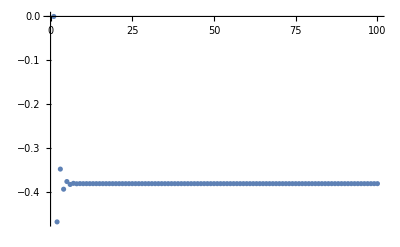

```mathematica
ListPlot[%59]
```

```mathematica
Apply[Log,Abs[#]]&/@Out[58]
```

{0,Log[-Log[3/2]/Log[1/2 (-1+√5)]]/Log[-Log[2]/Log[1/2 (-1+√5)]],Log[-Log[5/3]/Log[1/2 (-1+√5)]]/Log[-Log[3/2]/Log[1/2 (-1+√5)]],Log[-Log[8/5]/Log[1/2 (-1+√5)]]/Log[-Log[5/3]/Log[1/2 (-1+√5)]],Log[-Log[13/8]/Log[1/2 (-1+√5)]]/Log[-Log[8/5]/Log[1/2 (-1+√5)]],Log[-Log[21/13]/Log[1/2 (-1+√5)]]/Log[-Log[13/8]/Log[1/2 (-1+√5)]],Log[-Log[34/21]/Log[1/2 (-1+√5)]]/Log[-Log[21/13]/Log[1/2 (-1+√5)]],Log[-Log[55/34]/Log[1/2 (-1+√5)]]/Log[-Log[34/21]/Log[1/2 (-1+√5)]],Log[-Log[89/55]/Log[1/2 (-1+√5)]]/Log[-Log[55/34]/Log[1/2 (-1+√5)]],Log[-Log[144/89]/Log[1/2 (-1+√5)]]/Log[-Log[89/55]/Log[1/2 (-1+√5)]],Log[-Log[233/144]/Log[1/2 (-1+√5)]]/Log[-Log[144/89]/Log[1/2 (-1+√5)]],Log[-Log[377/233]/Log[1/2 (-1+√5)]]/Log[-Log[233/144]/Log[1/2 (-1+√5)]],Log[-Log[610/377]/Log[1/2 (-1+√5)]]/Log[-Log[377/233]/Log[1/2 (-1+√5)]],Log[-Log[987/610]/Log[1/2 (-1+√5)]]/Log[-Log[610/377]/Log[1/2 (-1+√5)]],Log[-Log[1597/987]/Log[1/2 (-1+√5)]]/Log[-Log[987/610]/Log[1/2 (-1+√5)]],Log[-Log[2584/1597]/Log[1/2 (-1+√5)]]/Log[-Log[1597/987]/Log[1/2 (-1+√5)]],Log[-Log[4181/2584]/Log[1/2 (-1+√5)]]/Log[-Log[2584/1597]/Log[1/2 (-1+√5)]],Log[-Log[6765/4181]/Log[1/2 (-1+√5)]]/Log[-Log[4181/2584]/Log[1/2 (-1+√5)]],Log[-Log[10946/6765]/Log[1/2 (-1+√5)]]/Log[-Log[6765/4181]/Log[1/2 (-1+√5)]],Log[-Log[17711/10946]/Log[1/2 (-1+√5)]]/Log[-Log[10946/6765]/Log[1/2 (-1+√5)]],Log[-Log[28657/17711]/Log[1/2 (-1+√5)]]/Log[-Log[17711/10946]/Log[1/2 (-1+√5)]],Log[-Log[46368/28657]/Log[1/2 (-1+√5)]]/Log[-Log[28657/17711]/Log[1/2 (-1+√5)]],Log[-Log[75025/46368]/Log[1/2 (-1+√5)]]/Log[-Log[46368/28657]/Log[1/2 (-1+√5)]],Log[-Log[121393/75025]/Log[1/2 (-1+√5)]]/Log[-Log[75025/46368]/Log[1/2 (-1+√5)]],Log[-Log[196418/121393]/Log[1/2 (-1+√5)]]/Log[-Log[121393/75025]/Log[1/2 (-1+√5)]],Log[-Log[317811/196418]/Log[1/2 (-1+√5)]]/Log[-Log[196418/121393]/Log[1/2 (-1+√5)]],Log[-Log[514229/317811]/Log[1/2 (-1+√5)]]/Log[-Log[317811/196418]/Log[1/2 (-1+√5)]],Log[-Log[832040/514229]/Log[1/2 (-1+√5)]]/Log[-Log[514229/317811]/Log[1/2 (-1+√5)]],Log[-Log[1346269/832040]/Log[1/2 (-1+√5)]]/Log[-Log[832040/514229]/Log[1/2 (-1+√5)]],Log[-Log[2178309/1346269]/Log[1/2 (-1+√5)]]/Log[-Log[1346269/832040]/Log[1/2 (-1+√5)]],Log[-Log[3524578/2178309]/Log[1/2 (-1+√5)]]/Log[-Log[2178309/1346269]/Log[1/2 (-1+√5)]],Log[-Log[5702887/3524578]/Log[1/2 (-1+√5)]]/Log[-Log[3524578/2178309]/Log[1/2 (-1+√5)]],Log[-Log[9227465/5702887]/Log[1/2 (-1+√5)]]/Log[-Log[5702887/3524578]/Log[1/2 (-1+√5)]],Log[-Log[14930352/9227465]/Log[1/2 (-1+√5)]]/Log[-Log[9227465/5702887]/Log[1/2 (-1+√5)]],Log[-Log[24157817/14930352]/Log[1/2 (-1+√5)]]/Log[-Log[14930352/9227465]/Log[1/2 (-1+√5)]],Log[-Log[39088169/24157817]/Log[1/2 (-1+√5)]]/Log[-Log[24157817/14930352]/Log[1/2 (-1+√5)]],Log[-Log[63245986/39088169]/Log[1/2 (-1+√5)]]/Log[-Log[39088169/24157817]/Log[1/2 (-1+√5)]],Log[-Log[102334155/63245986]/Log[1/2 (-1+√5)]]/Log[-Log[63245986/39088169]/Log[1/2 (-1+√5)]],Log[-Log[165580141/102334155]/Log[1/2 (-1+√5)]]/Log[-Log[102334155/63245986]/Log[1/2 (-1+√5)]],Log[-Log[267914296/165580141]/Log[1/2 (-1+√5)]]/Log[-Log[165580141/102334155]/Log[1/2 (-1+√5)]],Log[-Log[433494437/267914296]/Log[1/2 (-1+√5)]]/Log[-Log[267914296/165580141]/Log[1/2 (-1+√5)]],Log[-Log[701408733/433494437]/Log[1/2 (-1+√5)]]/Log[-Log[433494437/267914296]/Log[1/2 (-1+√5)]],Log[-Log[1134903170/701408733]/Log[1/2 (-1+√5)]]/Log[-Log[701408733/433494437]/Log[1/2 (-1+√5)]],Log[-Log[1836311903/1134903170]/Log[1/2 (-1+√5)]]/Log[-Log[1134903170/701408733]/Log[1/2 (-1+√5)]],Log[-Log[2971215073/1836311903]/Log[1/2 (-1+√5)]]/Log[-Log[1836311903/1134903170]/Log[1/2 (-1+√5)]],Log[-Log[4807526976/2971215073]/Log[1/2 (-1+√5)]]/Log[-Log[2971215073/1836311903]/Log[1/2 (-1+√5)]],Log[-Log[7778742049/4807526976]/Log[1/2 (-1+√5)]]/Log[-Log[4807526976/2971215073]/Log[1/2 (-1+√5)]],Log[-Log[12586269025/7778742049]/Log[1/2 (-1+√5)]]/Log[-Log[7778742049/4807526976]/Log[1/2 (-1+√5)]],Log[-Log[20365011074/12586269025]/Log[1/2 (-1+√5)]]/Log[-Log[12586269025/7778742049]/Log[1/2 (-1+√5)]],Log[-Log[32951280099/20365011074]/Log[1/2 (-1+√5)]]/Log[-Log[20365011074/12586269025]/Log[1/2 (-1+√5)]],Log[-Log[53316291173/32951280099]/Log[1/2 (-1+√5)]]/Log[-Log[32951280099/20365011074]/Log[1/2 (-1+√5)]],Log[-Log[86267571272/53316291173]/Log[1/2 (-1+√5)]]/Log[-Log[53316291173/32951280099]/Log[1/2 (-1+√5)]],Log[-Log[139583862445/86267571272]/Log[1/2 (-1+√5)]]/Log[-Log[86267571272/53316291173]/Log[1/2 (-1+√5)]],Log[-Log[225851433717/139583862445]/Log[1/2 (-1+√5)]]/Log[-Log[139583862445/86267571272]/Log[1/2 (-1+√5)]],Log[-Log[365435296162/225851433717]/Log[1/2 (-1+√5)]]/Log[-Log[225851433717/139583862445]/Log[1/2 (-1+√5)]],Log[-Log[591286729879/365435296162]/Log[1/2 (-1+√5)]]/Log[-Log[365435296162/225851433717]/Log[1/2 (-1+√5)]],Log[-Log[956722026041/591286729879]/Log[1/2 (-1+√5)]]/Log[-Log[591286729879/365435296162]/Log[1/2 (-1+√5)]],Log[-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)]]/Log[-Log[956722026041/591286729879]/Log[1/2 (-1+√5)]],Log[-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)]]/Log[-Log[1548008755920/956722026041]/Log[1/2 (-1+√5)]],Log[-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)]]/Log[-Log[2504730781961/1548008755920]/Log[1/2 (-1+√5)]],Log[-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)]]/Log[-Log[4052739537881/2504730781961]/Log[1/2 (-1+√5)]],Log[-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)]]/Log[-Log[6557470319842/4052739537881]/Log[1/2 (-1+√5)]],Log[-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)]]/Log[-Log[10610209857723/6557470319842]/Log[1/2 (-1+√5)]],Log[-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)]]/Log[-Log[17167680177565/10610209857723]/Log[1/2 (-1+√5)]],Log[-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)]]/Log[-Log[27777890035288/17167680177565]/Log[1/2 (-1+√5)]],Log[-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)]]/Log[-Log[44945570212853/27777890035288]/Log[1/2 (-1+√5)]],Log[-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)]]/Log[-Log[72723460248141/44945570212853]/Log[1/2 (-1+√5)]],Log[-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)]]/Log[-Log[117669030460994/72723460248141]/Log[1/2 (-1+√5)]],Log[-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)]]/Log[-Log[190392490709135/117669030460994]/Log[1/2 (-1+√5)]],Log[-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)]]/Log[-Log[308061521170129/190392490709135]/Log[1/2 (-1+√5)]],Log[-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)]]/Log[-Log[498454011879264/308061521170129]/Log[1/2 (-1+√5)]],Log[-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)]]/Log[-Log[806515533049393/498454011879264]/Log[1/2 (-1+√5)]],Log[-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)]]/Log[-Log[1304969544928657/806515533049393]/Log[1/2 (-1+√5)]],Log[-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)]]/Log[-Log[2111485077978050/1304969544928657]/Log[1/2 (-1+√5)]],Log[-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)]]/Log[-Log[3416454622906707/2111485077978050]/Log[1/2 (-1+√5)]],Log[-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)]]/Log[-Log[5527939700884757/3416454622906707]/Log[1/2 (-1+√5)]],Log[-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)]]/Log[-Log[8944394323791464/5527939700884757]/Log[1/2 (-1+√5)]],Log[-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)]]/Log[-Log[14472334024676221/8944394323791464]/Log[1/2 (-1+√5)]],Log[-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)]]/Log[-Log[23416728348467685/14472334024676221]/Log[1/2 (-1+√5)]],Log[-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)]]/Log[-Log[37889062373143906/23416728348467685]/Log[1/2 (-1+√5)]],Log[-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)]]/Log[-Log[61305790721611591/37889062373143906]/Log[1/2 (-1+√5)]],Log[-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)]]/Log[-Log[99194853094755497/61305790721611591]/Log[1/2 (-1+√5)]],Log[-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)]]/Log[-Log[160500643816367088/99194853094755497]/Log[1/2 (-1+√5)]],Log[-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)]]/Log[-Log[259695496911122585/160500643816367088]/Log[1/2 (-1+√5)]],Log[-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)]]/Log[-Log[420196140727489673/259695496911122585]/Log[1/2 (-1+√5)]],Log[-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)]]/Log[-Log[679891637638612258/420196140727489673]/Log[1/2 (-1+√5)]],Log[-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)]]/Log[-Log[1100087778366101931/679891637638612258]/Log[1/2 (-1+√5)]],Log[-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)]]/Log[-Log[1779979416004714189/1100087778366101931]/Log[1/2 (-1+√5)]],Log[-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)]]/Log[-Log[2880067194370816120/1779979416004714189]/Log[1/2 (-1+√5)]],Log[-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)]]/Log[-Log[4660046610375530309/2880067194370816120]/Log[1/2 (-1+√5)]],Log[-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)]]/Log[-Log[7540113804746346429/4660046610375530309]/Log[1/2 (-1+√5)]],Log[-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)]]/Log[-Log[12200160415121876738/7540113804746346429]/Log[1/2 (-1+√5)]],Log[-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)]]/Log[-Log[19740274219868223167/12200160415121876738]/Log[1/2 (-1+√5)]],Log[-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)]]/Log[-Log[31940434634990099905/19740274219868223167]/Log[1/2 (-1+√5)]],Log[-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)]]/Log[-Log[51680708854858323072/31940434634990099905]/Log[1/2 (-1+√5)]],Log[-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)]]/Log[-Log[83621143489848422977/51680708854858323072]/Log[1/2 (-1+√5)]],Log[-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)]]/Log[-Log[135301852344706746049/83621143489848422977]/Log[1/2 (-1+√5)]],Log[-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)]]/Log[-Log[218922995834555169026/135301852344706746049]/Log[1/2 (-1+√5)]],Log[-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)]]/Log[-Log[354224848179261915075/218922995834555169026]/Log[1/2 (-1+√5)]],Log[-Log[927372692193078999176/573147844013817084101]/Log[1/2 (-1+√5)]]/Log[-Log[573147844013817084101/354224848179261915075]/Log[1/2 (-1+√5)]]}

```mathematica
ListPlot[%61]
```

-Graphics-